## A notebook to plot the population time-evolution of a three level system and dark resonance.

### Notebook setup

```mathematica
Remove["Global`*"] (*Clears all variables*)

padding={{70, 10}, {50, 10}}; (*Space around plots*)
size=500;   (*Size of plots*)

SetOptions[Plot,BaseStyle->{FontFamily->"Optima",FontSize->16},PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Thick},{Orange,Thick},{Magenta,Thick}},TicksStyle->Directive[Black,10],Frame->True,ImagePadding->padding,ImageSize->size]; (*Sets Plots to have a certain look*)

SetOptions[ListPlot,BaseStyle->{FontFamily->"Optima",FontSize->16},PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Thick},{Orange,Thick},{Magenta,Thick}},TicksStyle->Directive[Black,10],Frame->True,Joined->True,ImagePadding->padding,ImageSize->size];  (*Sets ListPlots to have a certain look*)

messageHandler=If[Last[#],Abort[]]&;
Internal`AddHandler["Message",messageHandler];
```

### Units

```mathematica
μs=10^-6;
kHz=10^3;
MHz=10^6; 
GHz=10^9;
```

### Parameters

```mathematica
Δp=2π  0MHz; 
Δs=.;
τp = 2 μs;
Γ= 2π 20 MHz;
Ωp0=2π 651 kHz √(0.564/0.141);
Ωs0=2π 200MHz (0.085/0.33)√(redPower/6) ;(*triplet fraction in v=22 is 0.085, in v=26 it is 0.33*)
Ωp[t_]=Piecewise[{{Ωp0,1μs<t<1μs+τp}},0];
Ωs[t_]=Ωs0;
simTime=10μs;
simΔ = 30 MHz;
```

### Hamiltonian and solving the Schrodinger equation

```mathematica
pops[Δs0_,redPower0_,bEndTime_]:=Module[{Δs=Δs0,end=bEndTime,red=redPower0},
H[t_]=({{0, 0, -Ωp[t]}, {0, -(Δp-Δs), -Ωs[t]}, {-Ωp[t], -Ωs[t], -Δp-ⅈ Γ/2}})/.redPower->red;
ψ[t_]={c1[t],c2[t],c3[t]};init=ψ[0]=={1,0,0};SE=ⅈ ψ'[t]==H[t].ψ[t];
sols=NDSolve[{SE,init},{c1,c2,c3},{t,simTime},PrecisionGoal->9,Method->"StiffnessSwitching"];{p1,p2,p3}=Abs[#[t μs]/.sols]^2&/@{c1,c2,c3};
If[end,(#[[1]]/.t->simTime/μs)&/@{p1,p2,p3},Table[{τ,#[[1]]/.t-> τ }&/@{p1,p2,p3},{τ,0,simTime/μs,1/1000 simTime/μs}]ᵀ
]]
```

### Plot code

```mathematica
plot1=ListPlot[Table[{Δsi/MHz,pops[2π Δsi,#,True][[1]]},{Δsi,-simΔ,simΔ,simΔ/100}]&/@Range[0.1,1,.5],FrameLabel->{"Δs (MHz)","Survival"},PlotRange->{0,1},PlotLegends->Range[0.1,1,.5],PlotLabel->"Dark resonance for various red powers (mW)"];

plot2=ListPlot[pops[2π 10 MHz,0.1,False],Frame-> True,FrameLabel->{"time (μs)","population"},PlotRange->{0,1},PlotLegends->{"Feshbach","Ground","V=22"},PlotLabel->"Population over time"];
plot3=Plot[{Ωp[t μs]/(2π MHz),Ωs[t μs]/(2π MHz)/.redPower->0.1},{t,0,simTime/μs},FrameLabel->{"time (μs)","Ω (MHz)"},PlotLegends->{"Ωp","Ωs"},Filling->False,PlotLabel->"Pulses over time"];
```

### Plot

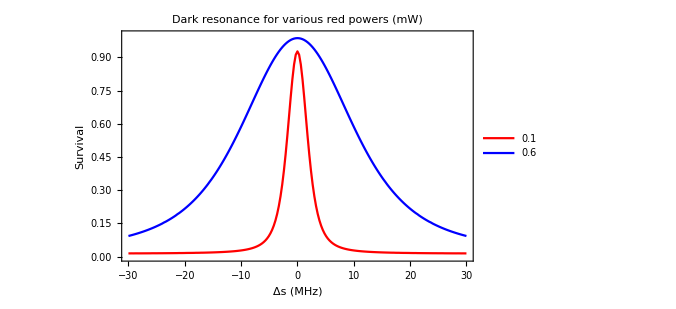
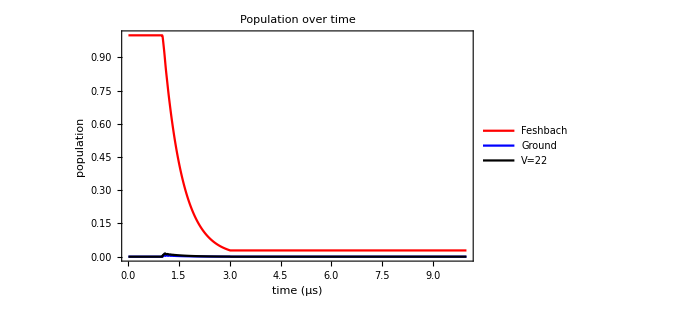
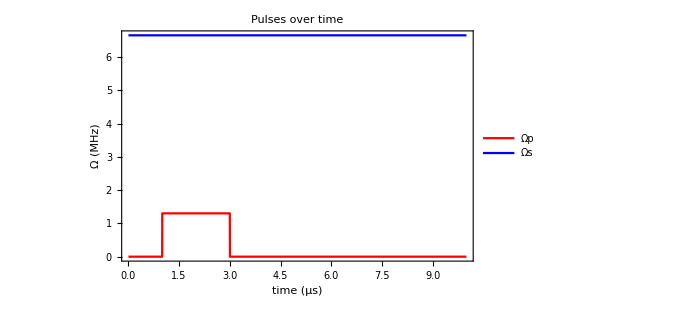
-Graphics- | -Graphics-
 | -Graphics-

```mathematica
TableForm[({{plot1, plot2}, {"", plot3}})]
```

```mathematica
data=Table[{Δsi/MHz,pops[2π Δsi,0.1,True][[1]]},{Δsi,-simΔ,simΔ,simΔ/100}];
```

```mathematica
FindFit[data,(A Exp[-1/2 (x/σ)^2])/(σ √(2 π)),{σ,A},x]
FindFit[data,A/(x^2+(γ/2)^2),{A,γ},x]
```

{σ→2.02032,A→4.43231}

{A→3.50583,γ→3.81659}

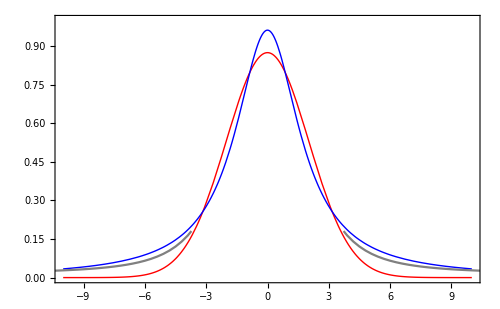

```mathematica
Show[Plot[{Evaluate[(A Exp[-1/2 (x/σ)^2])/(σ √(2 π))/.FindFit[data,(A Exp[-1/2 (x/σ)^2])/(σ √(2 π)),{σ,A},x]],Evaluate[A/(x^2+(γ/2)^2)/.FindFit[data,A/(x^2+(γ/2)^2),{A,γ},x]]},{x,-10,10},PlotRange->{0,1}],ListPlot[data,PlotStyle->Gray]]
```